```mathematica
Master equation for Raman- 3 level system
```

```mathematica
α = 0.6; ωR = 3 10^8*(2 Pi)/(455 10^-9);Γ = 1.84 10^6; Ωn = 2 Pi 30.6 10^3;δ1 = 1; δ2 = 1; δ12 = 0; η = 0.2;n = 1;hbar = 1.0545718×10^-34;
λ = 455.527 10^-9 ; Int = 180 10^-3/(10^-4); h = 2 Pi *hbar; c = 2.997 10^8;
ΩR = Sqrt[(3 λ^3 Γ Int)/(2 Pi h c)];
```

```mathematica
Clear[α, η]
```

```mathematica
H = hbar/2({{-2 δ1, Ωn, 0}, {Ωn, 0, ΩR}, {0, ΩR, -2 δ2}})
```

{{-1.05457×10^-34,1.01379×10^-29,0.},{1.01379×10^-29,0.,2.14625×10^-27},{0.,2.14625×10^-27,-1.05457×10^-34}}

```mathematica
Γ1 = α η^2 n Γ
Γ2 = (1-α)(1-η^2(2n - 1))Γ
```

44160.

706560.

```mathematica
Γ
```

4.05×10^6

```mathematica
Γo = Γ - Γ1 - Γ2;
```

```mathematica
L = ({{Γ1 ρ33[t], 0, -Γ/2 ρ13[t]}, {0, Γ2 ρ33[t], -Γ/2 ρ23[t]}, {-Γ/2 ρ31[t], -Γ/2 ρ32[t], -Γ ρ33[t]}})
```

{{44160. ρ33[t],0,-920000. ρ13[t]},{0,706560. ρ33[t],-920000. ρ23[t]},{-920000. ρ31[t],-920000. ρ32[t],-1.84×10^6 ρ33[t]}}

```mathematica
ρe[t_] := ({{ρ11[t], ρ12[t], ρ13[t]}, {ρ21[t], ρ22[t], ρ23[t]}, {ρ31[t], ρ32[t], ρ33[t]}})
```

```mathematica
dρdt =(-ⅈ/hbar(H. ρe[t]- ρe[t]. H)+L)//FullSimplify
```

{{(0.-9.48252×10^33 ⅈ) (0.-1.01379×10^-29 ρ12[t]+1.01379×10^-29 ρ21[t])+44160. ρ33[t],(0.-9.48252×10^33 ⅈ) (0.-1.01379×10^-29 ρ11[t]-1.05457×10^-34 ρ12[t]-2.14625×10^-27 ρ13[t]+1.01379×10^-29 ρ22[t]),-920000. ρ13[t]-(0.+9.48252×10^33 ⅈ) (0.-2.14625×10^-27 ρ12[t]+1.01379×10^-29 ρ23[t])},{(0.-9.48252×10^33 ⅈ) (0.+1.01379×10^-29 ρ11[t]+1.05457×10^-34 ρ21[t]-1.01379×10^-29 ρ22[t]+2.14625×10^-27 ρ31[t]),(0.-9.48252×10^33 ⅈ) (0.+1.01379×10^-29 ρ12[t]-1.01379×10^-29 ρ21[t]-2.14625×10^-27 ρ23[t]+2.14625×10^-27 ρ32[t])+706560. ρ33[t],-920000. ρ23[t]-(0.+9.48252×10^33 ⅈ) (0.+1.01379×10^-29 ρ13[t]-2.14625×10^-27 ρ22[t]+1.05457×10^-34 ρ23[t]+2.14625×10^-27 ρ33[t])},{-920000. ρ31[t]-(0.+9.48252×10^33 ⅈ) (0.+2.14625×10^-27 ρ21[t]-1.01379×10^-29 ρ32[t]),-920000. ρ32[t]-(0.+9.48252×10^33 ⅈ) (0.+2.14625×10^-27 ρ22[t]-1.01379×10^-29 ρ31[t]-1.05457×10^-34 ρ32[t]-2.14625×10^-27 ρ33[t]),(0.-9.48252×10^33 ⅈ) (0.+2.14625×10^-27 ρ23[t]-2.14625×10^-27 ρ32[t])-1.84×10^6 ρ33[t]}}

```mathematica
Clear[ρe]
```

```mathematica
ρe[t_] := ({{ρ11[t], ρ12[t], ρ13[t]}, {ρ21[t], ρ22[t], ρ23[t]}, {ρ31[t], ρ32[t], ρ33[t]}})
```

```mathematica
ρen= Flatten[({{ρ11, ρ12, ρ13}, {ρ21, ρ22, ρ23}, {ρ31, ρ32, ρ33}})]
```

{ρ11,ρ12,ρ13,ρ21,ρ22,ρ23,ρ31,ρ32,ρ33}

```mathematica
ρef = Flatten[ρe'[t]];
ρef2 = Flatten[ρe[t]];
dρdtf= Flatten[dρdt];
```

```mathematica
system = Flatten[Table[Part[ρef,j] == Part[dρdtf,j],{j,1,9,1}]];
```

```mathematica
numerical solution
```

```mathematica
ρe[t_] := {ρ11[t],ρ12[t],ρ13[t],ρ21[t],ρ22[t],ρ23[t],ρ31[t],ρ32[t],ρ33[t]};
init={ρ11[0] == 0, ρ12[0] == 0,ρ13[0] == 0,ρ21[0] == 0,ρ22[0] == 0,ρ23[0] == 0,ρ31[0] == 0,ρ32[0] == 0,ρ33[0] == 1};
Join[system,init]//N
```

{ρ11'[t]==(0.-9.48252×10^33 ⅈ) (0.-1.01379×10^-29 ρ12[t]+1.01379×10^-29 ρ21[t])+97200. ρ33[t],ρ12'[t]==(0.-9.48252×10^33 ⅈ) (0.-1.01379×10^-29 ρ11[t]-1.05457×10^-34 ρ12[t]-2.14625×10^-27 ρ13[t]+1.01379×10^-29 ρ22[t]),ρ13'[t]==-2.025×10^6 ρ13[t]-(0.+9.48252×10^33 ⅈ) (0.-2.14625×10^-27 ρ12[t]+1.01379×10^-29 ρ23[t]),ρ21'[t]==(0.-9.48252×10^33 ⅈ) (0.+1.01379×10^-29 ρ11[t]+1.05457×10^-34 ρ21[t]-1.01379×10^-29 ρ22[t]+2.14625×10^-27 ρ31[t]),ρ22'[t]==(0.-9.48252×10^33 ⅈ) (0.+1.01379×10^-29 ρ12[t]-1.01379×10^-29 ρ21[t]-2.14625×10^-27 ρ23[t]+2.14625×10^-27 ρ32[t])+1.5552×10^6 ρ33[t],ρ23'[t]==-2.025×10^6 ρ23[t]-(0.+9.48252×10^33 ⅈ) (0.+1.01379×10^-29 ρ13[t]-2.14625×10^-27 ρ22[t]+1.05457×10^-34 ρ23[t]+2.14625×10^-27 ρ33[t]),ρ31'[t]==-2.025×10^6 ρ31[t]-(0.+9.48252×10^33 ⅈ) (0.+2.14625×10^-27 ρ21[t]-1.01379×10^-29 ρ32[t]),ρ32'[t]==-2.025×10^6 ρ32[t]-(0.+9.48252×10^33 ⅈ) (0.+2.14625×10^-27 ρ22[t]-1.01379×10^-29 ρ31[t]-1.05457×10^-34 ρ32[t]-2.14625×10^-27 ρ33[t]),ρ33'[t]==(0.-9.48252×10^33 ⅈ) (0.+2.14625×10^-27 ρ23[t]-2.14625×10^-27 ρ32[t])-4.05×10^6 ρ33[t],ρ11[0.]==0.,ρ12[0.]==0.,ρ13[0.]==0.,ρ21[0.]==0.,ρ22[0.]==0.,ρ23[0.]==0.,ρ31[0.]==0.,ρ32[0.]==0.,ρ33[0.]==1.}

```mathematica
sol=NDSolve[Join[system&&init],ρen,{t,0,10*10^-1}, MaxSteps-> 10000]
```

{{ρ11→InterpolatingFunction[{{0., 1.}}, <>],ρ12→InterpolatingFunction[{{0., 1.}}, <>],ρ13→InterpolatingFunction[{{0., 1.}}, <>],ρ21→InterpolatingFunction[{{0., 1.}}, <>],ρ22→InterpolatingFunction[{{0., 1.}}, <>],ρ23→InterpolatingFunction[{{0., 1.}}, <>],ρ31→InterpolatingFunction[{{0., 1.}}, <>],ρ32→InterpolatingFunction[{{0., 1.}}, <>],ρ33→InterpolatingFunction[{{0., 1.}}, <>]}}

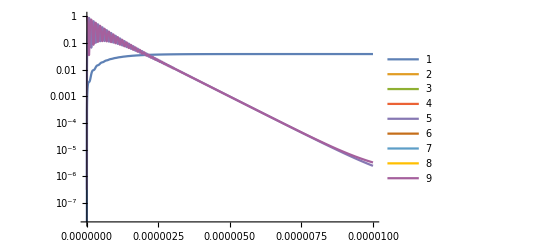

```mathematica
LogPlot[Evaluate[ρe[t]/.sol],{t,0,10*10^-6} , PlotRange -> All, PlotLegends -> Automatic, PlotRange -> {Automatic, {-2,2}}]
```

```mathematica
fun=ρ33/.First[sol]
```

InterpolatingFunction[{{0., 1.}}, <>]

```mathematica
fun[0.0601]
```

```mathematica
Re[fun[0.061]]
```

0.0050052

```mathematica
Solve[Re[fun[8 10^-6]] == Re[fun[2 10^-6]] Exp[-l *6 10^-6],l]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{l→1.2505×10^6}}

```mathematica
steady state solution
```

```mathematica
sol=DSolve[system,ρef2,t]
```

```mathematica
system = Table[0 == Part[dρdtf,j],{j,1,9,1}]
```

{0==1/2 ⅈ Ωn (ρ12[t]-ρ21[t])+n α Γ η^2 ρ33[t],0==1/2 ⅈ (Ωn ρ11[t]+2 δ1 ρ12[t]+ωR ρ13[t]-Ωn ρ22[t]),0==1/2 ⅈ (ωR ρ12[t]+(ⅈ Γ+2 δ1-2 δ2) ρ13[t]-Ωn ρ23[t]),0==-1/2 ⅈ (Ωn ρ11[t]+2 δ1 ρ21[t]-Ωn ρ22[t]+ωR ρ31[t]),0==-1/2 ⅈ (Ωn ρ12[t]-Ωn ρ21[t]+ωR (-ρ23[t]+ρ32[t]))+(-1+α) Γ (-1+(-1+2 n) η^2) ρ33[t],0==-1/2 ⅈ (Ωn ρ13[t]-ωR ρ22[t]-ⅈ Γ ρ23[t]+2 δ2 ρ23[t]+ωR ρ33[t]),0==-1/2 ⅈ (ωR ρ21[t]+(-ⅈ Γ+2 δ1-2 δ2) ρ31[t]-Ωn ρ32[t]),0==-1/2 ⅈ (ωR ρ22[t]-Ωn ρ31[t]-ⅈ Γ ρ32[t]-2 δ2 ρ32[t]-ωR ρ33[t]),0==-1/2 ⅈ ωR (ρ23[t]-ρ32[t])-Γ ρ33[t]}

```mathematica
system
```

```mathematica
Solve[system, ρef2]
```

{{ρ11[t]→0,ρ12[t]→0,ρ13[t]→0,ρ21[t]→0,ρ22[t]→0,ρ23[t]→0,ρ31[t]→0,ρ32[t]→0,ρ33[t]→0}}

```mathematica
no steady state solution as system is not closed, one can look at solutions with constant decay rates instead
```

```mathematica
H = hbar/2({{-2 δ1, Ωn, 0}, {Ωn, 0, ωR}, {0, ωR, -2 δ2}})
```

{{-hbar δ1,(hbar Ωn)/2,0},{(hbar Ωn)/2,0,(hbar ωR)/2},{0,(hbar ωR)/2,-hbar δ2}}

```mathematica
Γ1 = αeff  Γ;
Γ2 =  (1-αeff) Γ; Clear[Γ, ωR, n, η, hbar, Ωn, δ1, δ2, δ12]
```

```mathematica
L = ({{Γ1 ρ33[t], 0, -Γ/2 ρ13[t]}, {0, Γ2 ρ33[t], -Γ/2 ρ23[t]}, {-Γ/2 ρ31[t], -Γ/2 ρ32[t], -Γ ρ33[t]}})
```

{{αeff Γ ρ33[t],0,-1/2 Γ ρ13[t]},{0,(1-αeff) Γ ρ33[t],-1/2 Γ ρ23[t]},{-1/2 Γ ρ31[t],-1/2 Γ ρ32[t],-Γ ρ33[t]}}

```mathematica
ρe[t_] := ({{ρ11[t], ρ12[t], ρ13[t]}, {ρ21[t], ρ22[t], ρ23[t]}, {ρ31[t], ρ32[t], ρ33[t]}})
```

```mathematica
(*dρdt = -1/hbar(H. ρe[t]- ρe[t]. H)+ L //FullSimplify*)
dρdt = -ⅈ/hbar(H. ρe[t]- ρe[t]. H) //FullSimplify
```

{{1/2 ⅈ Ωn (ρ12[t]-ρ21[t]),1/2 ⅈ (Ωn ρ11[t]+2 δ1 ρ12[t]+ωR ρ13[t]-Ωn ρ22[t]),1/2 ⅈ (ωR ρ12[t]+2 (δ1-δ2) ρ13[t]-Ωn ρ23[t])},{-1/2 ⅈ (Ωn ρ11[t]+2 δ1 ρ21[t]-Ωn ρ22[t]+ωR ρ31[t]),-1/2 ⅈ (Ωn ρ12[t]-Ωn ρ21[t]+ωR (-ρ23[t]+ρ32[t])),-1/2 ⅈ (Ωn ρ13[t]-ωR ρ22[t]+2 δ2 ρ23[t]+ωR ρ33[t])},{-1/2 ⅈ (ωR ρ21[t]+2 (δ1-δ2) ρ31[t]-Ωn ρ32[t]),1/2 ⅈ (-ωR ρ22[t]+Ωn ρ31[t]+2 δ2 ρ32[t]+ωR ρ33[t]),-1/2 ⅈ ωR (ρ23[t]-ρ32[t])}}

```mathematica
ρef = Flatten[ρe'[t]];
ρef2 = Flatten[ρe[t]];
dρdtf= Flatten[dρdt];
system = Table[0 == Part[dρdtf,j],{j,1,9,1}]//FullSimplify
```

{Ωn ρ12[t]==Ωn ρ21[t],Ωn ρ11[t]+2 δ1 ρ12[t]+ωR ρ13[t]==Ωn ρ22[t],ωR ρ12[t]+2 (δ1-δ2) ρ13[t]==Ωn ρ23[t],Ωn ρ11[t]+2 δ1 ρ21[t]+ωR ρ31[t]==Ωn ρ22[t],Ωn ρ12[t]+ωR ρ32[t]==Ωn ρ21[t]+ωR ρ23[t],Ωn ρ13[t]+2 δ2 ρ23[t]+ωR ρ33[t]==ωR ρ22[t],ωR ρ21[t]+2 (δ1-δ2) ρ31[t]==Ωn ρ32[t],ωR ρ22[t]==Ωn ρ31[t]+2 δ2 ρ32[t]+ωR ρ33[t],ωR ρ23[t]==ωR ρ32[t]}

```mathematica
Solve[system, ρef2]//FullSimplify
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{ρ11[t]→ρ22[t]+((4 δ1 (-δ1+δ2)+ωR^2) ρ12[t]-Ωn ωR ρ23[t])/(2 (δ1-δ2) Ωn),ρ13[t]→(-ωR ρ12[t]+Ωn ρ23[t])/(2 (δ1-δ2)),ρ21[t]→ρ12[t],ρ31[t]→(-ωR ρ12[t]+Ωn ρ23[t])/(2 (δ1-δ2)),ρ32[t]→ρ23[t],ρ33[t]→ρ22[t]-(2 δ2 ρ23[t])/ωR+(Ωn ωR ρ12[t]-Ωn^2 ρ23[t])/(2 δ1 ωR-2 δ2 ωR)}}

```mathematica
null := ({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})
```

```mathematica
Solve[null == dρdt, ρe]//FullSimplify
```

{}